3.10: 6, 28, 32

6: Find the linear approximation of the function

```mathematica
g[x_]:=Surd[1+x,3]
```

at a = 0 and use it to approximate the cube root of 0.95 and 1.1. Illustrate by plotting g and its tangent line.

Here’s the linear approximation:

```mathematica
L[x_]:= g[0] + g'[0](x-0)
```

To approximate the cube roots of 0.95 and 1.1, we’ll compute L(-0.05) and L(0.1):

```mathematica
L[-0.05]
```

0.983333

```mathematica
L[0.1]
```

1.03333

How close are we?

```mathematica
Abs[Surd[0.95,3]-g[-0.05]]
Abs[Surd[1.1,3]-g[-0.1]]
```

0.

0.0667907

Pretty close! Here’s the plot:

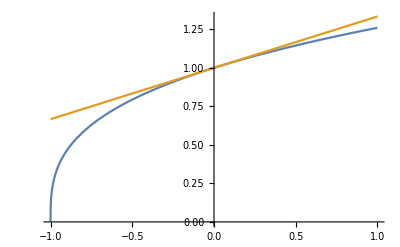

```mathematica
Plot[{g[x],L[x]},{x,-1,1}]
```

28: Use a linear approximation to estimate the square root of 99.8. We’ll compute the linear approximation to

```mathematica
s[x_] :=Sqrt[x]
```

at the point a = 100.

```mathematica
L28[x_]:= s[100] + s'[100](x-100)
```

Finally, compute the approximation:

```mathematica
L28[99.8]
```

9.99

How close is this?

```mathematica
Abs[s[99.8] - L28[99.8]]
```

5.00501×10^-6

Very close!

32: Consider the following three functions

```mathematica
f[x_]:=(x-1)^2
g[x_]:=E^(-2x)
h[x_]:=1+Log[1-2x]
```

a) Find the linearizations of each at a = 0. To do so, we need each of the functions at 0:

```mathematica
f[0]
g[0]
h[0]
```

1

1

1

And their derivatives at 0:

```mathematica
f'[0]
g'[0]
h'[0]
```

-2

-2

-2

They all have the same linearization!

```mathematica
L32[x_]:= 1-2x
```

I guess they all have the same tangent line at x=0. b): Let’s plot.

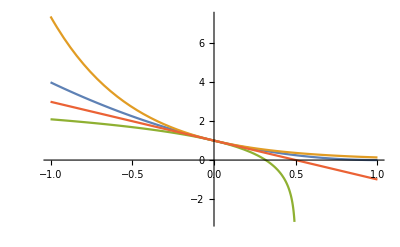

```mathematica
Plot[{f[x],g[x],h[x],L32[x]},{x,-1,1}]
```

Which is which? If we click around in the context menu (in more...), we can enable the legend.

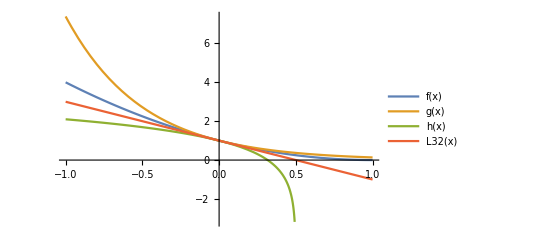

```mathematica
Plot[{f[x],g[x],h[x],L32[x]},{x,-1,1},PlotLegends->"Expressions"]
```

To which function is L32 the best approximation? The worst? It’s hard to tell from this picture. Let’s zoom in:

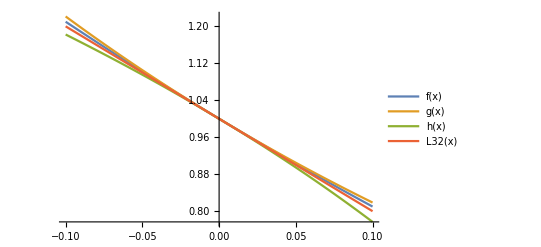

```mathematica
Plot[{f[x],g[x],h[x],L32[x]},{x,-.1,.1},PlotLegends->"Expressions"]
```

It looks like L32 is the best approximation to f(x) and the worst to h(x).